# Report Project 3

Course code: IV1500
Date: 24-10-2023

Seema Bashir, sfbashir@kth.se

Grade B Task

## Question1

Describe Europe as a graph and draw this as a labeled figure . Overlay this on a map of Europe . Use the convention that countries are nodes and the borders are edges . Assume that there is a connection between the following countries : Great Britain and France, Great Britain and Netherlands, Great Britain and Ireland, Great Britain and {Guernsey, Jersey, Isle of Man}, Faroe Islands and Great Britain, Faroe Islands and Iceland, Faroe Islands and Denmark, Iceland and Norway, Norway and Svalbard, Iceland and Denmark, Denmark and Sweden, Italy and Malta, Greece and Cyprus .

Find out if the Europe graph is Hamilton and/or a Euler graph. What happens if you remove all vertices of degree one?

Calculate the chromatic polynomial and the chromatic number for the Europe graph

Color the graph using the chromatic number colors.

### Result

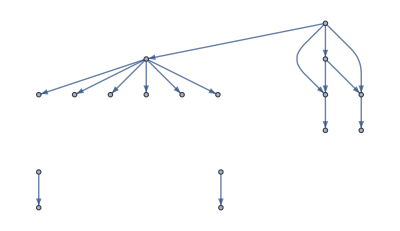
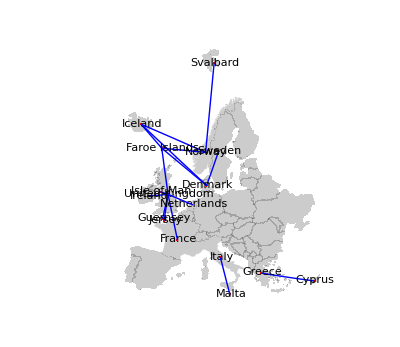
The primary objective is to analyze the properties of this network, particularly its connectivity. The data is represented as a graph, where the cities/regions are the vertices, and the connections between them are the edges. The graph is stored as an adjacency matrix, which indicates the presence or absence of edges between vertices.

An Eulerian graph is a graph where a path exists that traverses every edge exactly once and returns to the starting vertex. One important property of Eulerian graphs is that every vertex must have an even degree (an even number of edges incident to it). This property is crucial for a graph to be traversable following an Eulerian path.

Vertex Degrees: The first step in our analysis is to determine the degrees of each vertex, which represent the number of edges connected to each city/region.

Adjacency Matrix: We use an adjacency matrix to store the connectivity information. In this matrix, a value of 1 indicates the presence of an edge between two vertices, and 0 indicates no edge.

Eulerian Property: To determine if the graph is Eulerian, we examine the degrees of all vertices. If even a single vertex has an odd degree, the graph cannot be Eulerian.

In the code provided, we find that not all vertices in the graph have an even degree. This means there are cities or regions that are connected to an odd number of other cities or regions. As a result, the graph is not Eulerian because it does not satisfy the necessary condition of having all vertices with even degrees.

In terms of practical applications, this result suggests that there is no single path that can visit every connection exactly once and return to the starting point. This information is crucial for solving various routing and optimization problems.

The presence of cities or regions with odd degrees could indicate that certain areas have an unusual or uneven distribution of connections compared to others. This could have implications for transportation planning, infrastructure development, or communication networks.

While this specific analysis demonstrates that the graph is not Eulerian, it may still have other interesting properties or be useful for other types of analyses, such as finding the shortest path between specific cities.

Isolated Nodes:In the provided code,when analyzing the graph’s structure and connectivity,it becomes evident that there are certain isolated nodes (cities or regions).Isolated nodes are vertices that have no edges connecting them to the rest of the graph.This implies that there are cities or regions within the network that are not directly connected to any other locations.

The graph in the provided code is not a Hamiltonian graph because there is no Hamiltonian cycle, primarily due to the existence of isolated nodes. Additionally, the graph is not connected (sammanhängande), as there are certain cities or regions that are not directly reachable from others.

The presence of isolated nodes in the graph may signify that some cities or regions are not directly connected to the transportation or communication network represented by the graph. This could have practical implications for planning routes and infrastructure.

In terms of Hamiltonian graphs, the absence of a Hamiltonian cycle may indicate limitations in the ability to find a single route that covers all cities or regions exactly once and returns to the starting point.

(0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)


-Graphics-

-Graphics-

## Code

```mathematica
city={"United Kingdom","France","Netherlands","Ireland","Guernsey","Jersey","Isle of Man","Faroe Islands","Iceland","Denmark","Norway","Svalbard","Sweden","Italy","Malta","Greece","Cyprus"};

(*Define the connections using numeric labels*)
links={{1,{2,3,4,5,6,7}},{8,{1,9,10,11}},{9,{10,11}},{11,12},{10,13},{14,15},{16,17}};

(*Extract country coordinates*)
countryCoordinates=CountryData[#,"CenterCoordinates"]&/@city;

(*Create the adjacency matrix based on the connections*)
adjacencyMatrix=Table[0,{Length[city]},{Length[city]}];

Do[If[Head[links[[i,2]]]===List,(*If the connection is a list of cities,set adjacency values for each city in the list*)Do[adjacencyMatrix[[links[[i,1]],j]]=1,{j,links[[i,2]]}],(*If the connection is a single city,set the adjacency value for that city*)adjacencyMatrix[[links[[i,1]],links[[i,2]]]]=1],{i,Length[links]}];

adjacencyMatrix//MatrixForm

g=AdjacencyGraph[adjacencyMatrix];
g

v=VertexList[g];
e=EdgeList[g];

Options[geoGraph]={EdgeStyle->Black,VertexStyle->GeoStyling[None],VertexLabels->None,VertexLabelStyle->Black};

(*Adjust label positions and sizes*)
Module[{es=OptionValue[EdgeStyle],vs=OptionValue[VertexStyle],vl=OptionValue[VertexLabels],vls=OptionValue[VertexLabelStyle],lbl,Δ={0.2,0.4}},If[Length[vl]!=Length[v],vl=None];
lbl=If[vl===None,{},Join[{vls},MapThread[Text[#1,GeoPosition[#2+Δ],{1,1}]&,{vl,countryCoordinates}]];
Join[Join[{vs},(GeoDisk[countryCoordinates[[#1]],r]&)/@v],Join[{es},(GeoPath[{countryCoordinates[[#1[[1]]]],countryCoordinates[[#1[[2]]]]}]&)/@e],lbl]]];
r=10 10^3;
GeoGraphics[{Polygon[CountryData["Europe"]],geoGraph[v,e,𝕔,r,EdgeStyle->Blue,VertexStyle->GeoStyling[Red],VertexLabels->city]},GeoBackground->None,GeoProjection->"LambertAzimuthal"]
```

Grade A

## Question 2

In the guidance section 2.2, it was shown how relations between cities can be illustrated. Let us assume that each city represents a router that forwards data packets to their final destination. Your task this time is to create a tree that shows how data packets are routed so that each city can be reached by the information flow that (this time) is based on Stockholm.

```mathematica
city={"Abisko","Boden","Falun","Goteborg","Hoganas","Hudiksvall","Jonkoping","Kalmar","Kiruna","Lidkoping","Linkoping","Lulea","Lund","Malmo","Mariestad","Ostersund","Stockholm","Strangnas","Timra","Uppsala","Umea","Varberg","Visby"};

links={{15,18},{13,17},{3,16},{6,3},{18,6},{12,2},{15,11},{19,21},{7,8},{19,2},{7,4},{21,17},{17,11},{23,11},{10,7},{16,17},{10,20},{13,5},{3,17},{7,22},{15,10},{16,18},{11,16},{17,23},{18,17},{20,6},{11,7},{9,2},{3,20},{4,17},{19,17},{7,20},{22,4},{14,7},{15,17},{6,17},{20,5},{16,15},{11,3},{9,1},{4,10},{5,14},{6,16},{16,19},{13,8},{8,23},{16,10},{4,13},{2,16},{15,3},{20,18}};

city⟦links⟦2⟧⟧
```

Weight (cost) for the use of a link between the two cities is assumed to be inversely proportional to the free capacity of the link. Suppose, for example, the following available capacity:

	Stockholm | – | Göteborg | 100
Stockholm | – | Lund | 100
Göteborg | – | Lund | 50
Stockholm | – | Falun | 25
Stockholm | – | Östersund | 50
Östersund | - | Umeå | 25

## Code